```mathematica
y1[x_] = x + x^2 + x^3/4 + x^4/36 + x^5/576
```

x+x^2+x^3/4+x^4/36+x^5/576

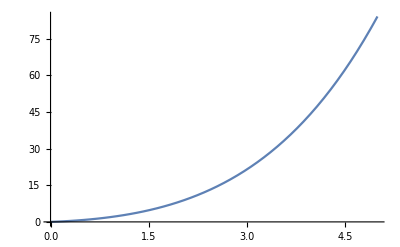

```mathematica
Plot [y1[x],{x, 0, 5}]
```

```mathematica
y2[x_] = y1[x] * Log[x]- 2*x^2-(3*x^3/4)- (11*x^4/108)
```

-2 x^2-(3 x^3)/4-(11 x^4)/108+(x+x^2+x^3/4+x^4/36+x^5/576) Log[x]

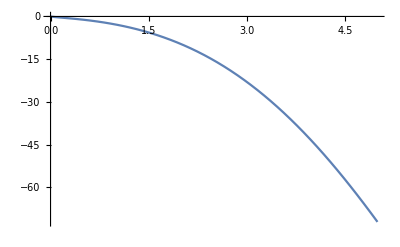

```mathematica
Plot[y2[x], {x, 0, 5}]
```

```mathematica
Plot[{y1[x],y2[x]},{x,0,5}, PlotLabels->Placed[Automatic, Right]]
```